## LUX Test Statistic (TS)

```mathematica
data= Import[NotebookDirectory[] <> "LUXdata/LUX-TS.txt", "Table"];
(*xval = data[[All,1]];
yval = data[[All,2]];
zval = data[[All, 3]];

nbins = 201;
data1 = Table[zval[[j + (i-1)*nbins]], {i, nbins}, {j,nbins}];
xval = xval[[1;;nbins^2;;nbins]];
yval = yval[[1;;nbins]];
TSInterp= ListInterpolation[data1, {xval, yval}, InterpolationOrder->{1,1}];*)

LUXTSInterp = Interpolation[data, InterpolationOrder->{1,1}];

ClearAll[LUXTS]
LUXTS[lm_?NumericQ, lλ_?NumericQ]:=LUXTSInterp[10^lm, 10^lλ] + 10^-10 Abs[lλ];
```

```mathematica
(*<<UnitConversion`*)
```

```mathematica
(*μ[mχ_]:=mχ 0.9315/(mχ + 0.9315);*)
```

```mathematica
(*λB[mχ_, σ_] := NNatural[(cm GeV)]Sqrt[σ 16 π mχ^2/μ[mχ]^2(0.9315)^2 Sum[YLUX[1][N1, N2][mχ], {N1, {"p","n"}},{N2,{"p","n"}}]]*)
```

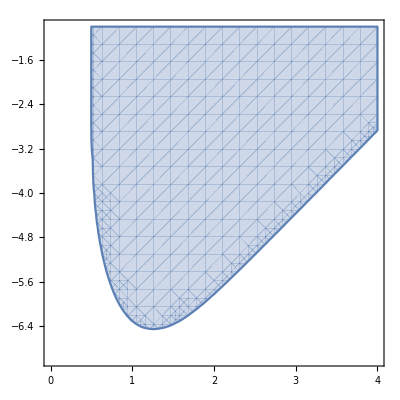

```mathematica
(*RegionPlot[LUXTS[lmx, lλ]  < Log[0.1], {lmx, Log10[1], 4}, {lλ, -7, -1}]*)
```

```mathematica
(*FindRoot[LUXTS[Log10[50], Log10[λB[50, 10^lσ]] ]== Log[0.1], {lσ, -47, -44}]*)
```

{lσ→-45.6722}

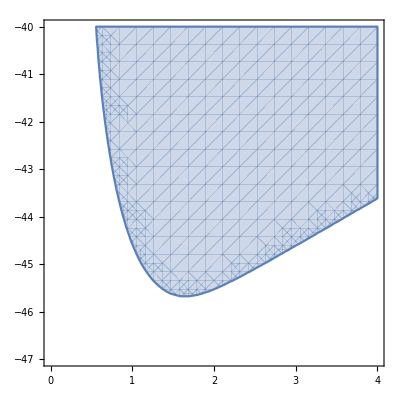

```mathematica
(*RegionPlot[LUXTS[lmx, Log10[λB[10^lmx, 10^lσ]] ]  < Log[0.1], {lmx, Log10[1], 4}, {lσ, -47, -40}]*)
```

## LUX Conversion Factors (Y)

Contact operators

```mathematica
opvals = {1, 3, 4, 5, 6, 7, 8, 9, 10, 11};
LUXYpp = Table[Import[NotebookDirectory[] <> "LUXdata/Y_LUX_" <> ToString[i]<> "_" <> ToString[j] <>"_pp.txt", "Table"], {i, opvals}, {j, opvals}];
LUXYpn = Table[Import[NotebookDirectory[] <> "LUXdata/Y_LUX_" <> ToString[i] <> "_" <> ToString[j] <>"_pn.txt", "Table"],{i, opvals}, {j, opvals}];
LUXYnn = Table[Import[NotebookDirectory[] <> "LUXdata/Y_LUX_" <> ToString[i] <> "_" <>ToString[j] <>"_nn.txt", "Table"], {i, opvals}, {j, opvals}];
```

```mathematica
LUXYintpp = Table[ListInterpolation[LUXYpp[[i,j]][[All,2]],LUXYpp[[i,j]][[All,1]], InterpolationOrder->{1}], {i,Length[opvals] }, {j, Length[opvals]}];
LUXYintpn = Table[ListInterpolation[LUXYpn[[i,j]][[All,2]],LUXYpn[[i,j]][[All,1]], InterpolationOrder->{1}], {i,Length[opvals] }, {j, Length[opvals]}];
LUXYintnn = Table[ListInterpolation[LUXYnn[[i,j]][[All,2]],LUXYnn[[i,j]][[All,1]], InterpolationOrder->{1}], {i,Length[opvals] }, {j, Length[opvals]}];
```

Long range operators

```mathematica
opvalsLR = {1,  4, 5, 6, 11};
LUXYppLR = Table[Import[NotebookDirectory[] <> "LUXdata/Y_LUX_" <> ToString[i]<> "_" <> ToString[j] <>"_LR_pp.txt", "Table"], {i, opvalsLR}, {j, opvalsLR}];
LUXYpnLR = Table[Import[NotebookDirectory[] <> "LUXdata/Y_LUX_" <> ToString[i] <> "_" <> ToString[j] <>"_LR_pn.txt", "Table"],{i, opvalsLR}, {j, opvalsLR}];
LUXYnnLR = Table[Import[NotebookDirectory[] <> "LUXdata/Y_LUX_" <> ToString[i] <> "_" <>ToString[j] <>"_LR_nn.txt", "Table"], {i, opvalsLR}, {j, opvalsLR}];
```

```mathematica
LUXYintppLR = Table[ListInterpolation[LUXYppLR[[i,j]][[All,2]],LUXYppLR[[i,j]][[All,1]], InterpolationOrder->{1}], {i,Length[opvalsLR] }, {j, Length[opvalsLR]}];
LUXYintpnLR = Table[ListInterpolation[LUXYpnLR[[i,j]][[All,2]],LUXYpnLR[[i,j]][[All,1]], InterpolationOrder->{1}], {i,Length[opvalsLR] }, {j, Length[opvalsLR]}];
LUXYintnnLR = Table[ListInterpolation[LUXYnnLR[[i,j]][[All,2]],LUXYnnLR[[i,j]][[All,1]], InterpolationOrder->{1}], {i,Length[opvalsLR ]}, {j, Length[opvalsLR]}];
```

```mathematica
ClearAll[YLUX]
YLUX[type_?StringQ][i1_, i2_][N1_, N2_][m_?NumericQ]:=
(
If[type == "Contact",
iop1 = Flatten[Position[opvals,i1]][[1]];
iop2 = Flatten[Position[opvals,i2]][[1]];
If[(N1 == "p")&&(N2 =="p"), Return[LUXYintpp[[iop1,iop2]][m]]];
If[(N1 == "p")&&(N2 =="n"), Return[LUXYintpn[[iop1,iop2]][m]]];
If[(N1 == "n")&&(N2 =="p"), Return[LUXYintpn[[iop1,iop2]][m]]];
If[(N1 == "n")&&(N2 =="n"), Return[LUXYintnn[[iop1,iop2]][m]]];
,
iop1 = Flatten[Position[opvalsLR,i1]][[1]];
iop2 = Flatten[Position[opvalsLR,i2]][[1]];
If[(N1 == "p")&&(N2 =="p"), Return[LUXYintppLR[[iop1,iop2]][m]]];
If[(N1 == "p")&&(N2 =="n"), Return[LUXYintpnLR[[iop1,iop2]][m]]];
If[(N1 == "n")&&(N2 =="p"), Return[LUXYintpnLR[[iop1,iop2]][m]]];
If[(N1 == "n")&&(N2 =="n"), Return[LUXYintnnLR[[iop1,iop2]][m]]];
]
)
```